# Математическа статистика 2024-2025 учебна година доц. Петър Копанов

пресмятане на основните числови характеристики (статистики) на извадка

вариационен ред на извадката:

№ | стойност
1 | 82.
2 | 93.
3 | 103.
4 | 107.
5 | 111.
6 | 116.
7 | 121.
8 | 124.
9 | 126.
10 | 127.
11 | 129.
12 | 137.
13 | 139.
14 | 139.
15 | 140.
16 | 141.
17 | 141.
18 | 147.
19 | 148.
20 | 149.
21 | 151.
22 | 152.
23 | 154.
24 | 155.
25 | 155.
26 | 156.
27 | 156.
28 | 157.
29 | 159.
30 | 160.
31 | 160.
32 | 162.
33 | 163.
34 | 164.
35 | 164.
36 | 164.
37 | 164.
38 | 166.
39 | 166.
40 | 166.
41 | 169.
42 | 169.
43 | 171.
44 | 173.
45 | 173.
46 | 174.
47 | 175.
48 | 176.
49 | 177.
50 | 177.
51 | 178.
52 | 180.
53 | 180.
54 | 181.
55 | 182.
56 | 182.
57 | 184.
58 | 186.
59 | 186.
60 | 187.
61 | 187.
62 | 189.
63 | 190.
64 | 192.
65 | 196.
66 | 199.
67 | 200.
68 | 202.
69 | 205.
70 | 205.
71 | 206.
72 | 207.
73 | 213.
74 | 214.
75 | 224.
76 | 227.
77 | 234.
78 | 235.
79 | 243.
80 | 251.

основни числови характеристики (статистики) на извадката:

обем на извадката (lenght) = 80

минимум на извадката (min) = 82.

максимум на извадката (max) = 251.

размах (range) на извадката  = 169.

средно (mean) = 168.663

дисперсия (variance) = 1140.63

средно отклонение(mean deviation) = 25.8125

стандартно отклонение (std dev) = 33.7732

асиметрия (skewness) = -0.0245536

ексцес (kurtosis) = 3.15144

медиана (median) = 167.5

медианно отклонение (median deviation) = 19.

средноквадратично отклонение(rms) = 171.969

qtl = {149.,187.}

quart = {150.,167.5,187.}

Графична визуализация на данните.  Построяване на хистограми и гладки хистограми

хистограма на извадката:

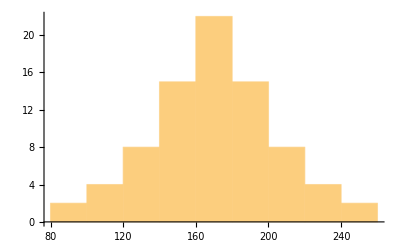

изгладена хистограма на извадката:

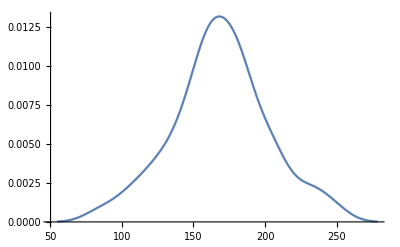

плътност на нормално разпределение, асоциирано с извадката:

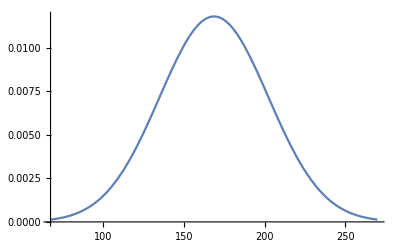

съвместни графики на изгладена хистограма на извадката и плътност на нормално разпределение, асоциирано с извадката:

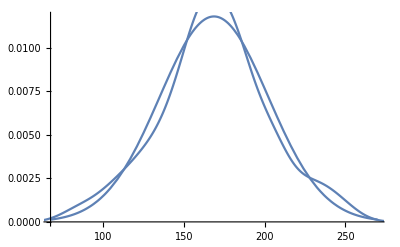

плътност на експоненциално разпределение, асоциирано с извадката:

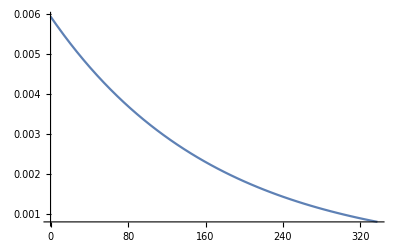

съвместни графики на изгладена хистограма на извадката и плътност на експоненциално разпределение асоциирано с извадката:

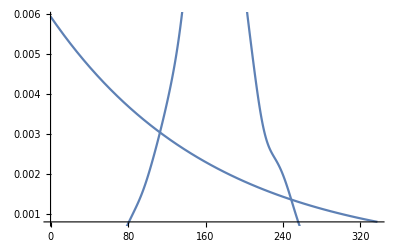

емпирична плътност  на извадката f_n(x):

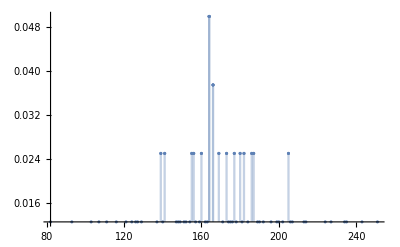

емпирична кумулативна функция на извадката F_n(x):

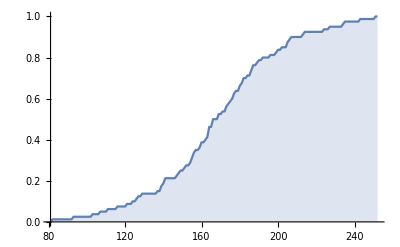

емпирична плътност f_n(x) и емпирична кумулативна функция на извадката F_n(x):

{-Graphics-,-Graphics-}

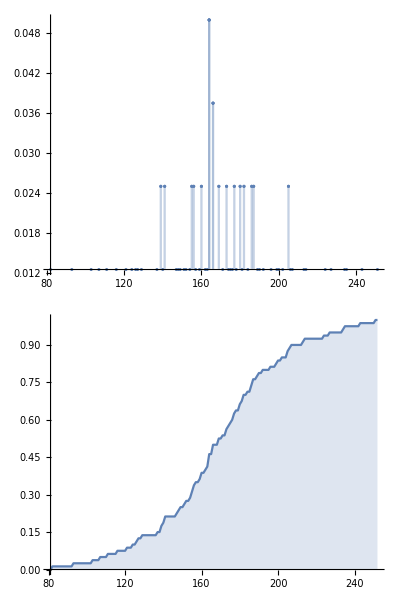

функция на разпределение на нормално разпределение, асоциирано с извадката и емпирична кумулативна функция на извадката F_n(x) :

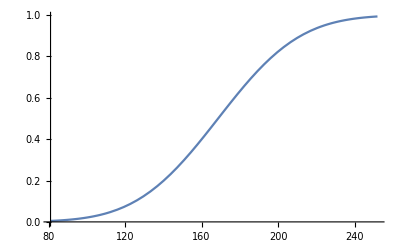
{-Graphics-,-Graphics-}

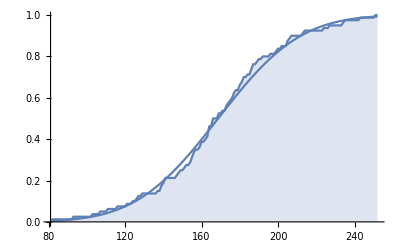

```mathematica
Clear["Global`*"]


	(*    Задаване на извадката   *) 

datex1={111.,103.,251.,169.,213.,140.,224.,205.,166.,202.,227.,160.,234.,137.,186.,184.,163.,157.,181.,207.,189.,159.,180.,160.,196.,82.,107.,148.,155.,206.,192.,180.,205.,121.,199.,173.,177.,169.,93.,182.,127.,126.,187.,166.,200.,190.,171.,151.,166.,156.,187.,174.,164.,214.,139.,141.,178.,177.,243.,176.,186.,173.,182.,164.,162.,235.,164.,154.,156.,124.,149.,147.,116.,139.,129.,152.,175.,164.,141.,155.};
	
(* препоръка: първо наберете данните в обикновен текстов редактор, след което ги копирайте на мястото на горните  *)
Print ["  "]
Print ["  "]

(* построяване вариационния ред на извадката : *)



Print ["                     :0432:0430:0440:0438:0430:0446:0438:043e:043d:0435:043d :0440:0435:0434 :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430:  "]

datex2= Sort [datex1] ;
datex3=Range [Length[datex1]];
datex4= Transpose[{datex3,datex2}];
TableForm[datex4, TableHeadings->{None, {"№", "стойност"}}]

 

(*   забележка: 
в  datex2,  datex4 са записани различни варианти на вариационния ред - без и със номера на елементите.  *)


Print ["  "]
Print ["  "]
Print["          :043e:0441:043d:043e:0432:043d:0438 :0447:0438:0441:043b:043e:0432:0438 :0445:0430:0440:0430:043a:0442:0435:0440:0438:0441:0442:0438:043a:0438 (:0441:0442:0430:0442:0438:0441:0442:0438:043a:0438) :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430: "]
Print ["  "]
Print["обем на извадката (lenght) = ",Length[datex1]]
Print["минимум на извадката (min) = ",Min[datex1]]
Print["максимум на извадката (max) = ",Max[datex1]]
Print["размах (range) на извадката  = ",Max[datex1]-Min[datex1]]
Print["средно (mean) = ",Mean[datex1]]
Print["дисперсия (variance) = ",Variance[datex1]]
Print["средно отклонение(mean deviation) = ",MeanDeviation[datex1]]
Print["стандартно отклонение (std dev) = ",StandardDeviation[datex1]]
Print["асиметрия (skewness) = ",Skewness[datex1]]
Print["ексцес (kurtosis) = ",Kurtosis[datex1]]
Print["медиана (median) = ",Median[datex1]]
Print["медианно отклонение (median deviation) = ",MedianDeviation[datex1]]
Print["средноквадратично отклонение(rms) = ",RootMeanSquare[datex1]]
Print["qtl = ",Quantile[datex1,{1/4,3/4}]]
Print["quart = ",Quartiles[datex1]]

	(*графично представяне на извадката*)

Print ["  "]
Print ["  "]
Print ["                       Графична визуализация на данните.  Построяване на хистограми и гладки хистограми    "]
Print ["  "]
Print ["  "]
Print["                         :0445:0438:0441:0442:043e:0433:0440:0430:043c:0430 :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430: "]
Print ["  "]
Histogram[datex1]
Print ["  "]
Print ["  "]
Print["                    :0438:0437:0433:043b:0430:0434:0435:043d:0430 :0445:0438:0441:0442:043e:0433:0440:0430:043c:0430 :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430: "]
Print ["  "]
SmoothHistogram[datex1]
Print ["  "]
Print ["  "]

	(* графично съпоставяне на изгладената хистограма на извадката с нормалното разпределение *)

Print["               :043f:043b:044a:0442:043d:043e:0441:0442 :043d:0430 :043d:043e:0440:043c:0430:043b:043d:043e :0440:0430:0437:043f:0440:0435:0434:0435:043b:0435:043d:0438:0435, :0430:0441:043e:0446:0438:0438:0440:0430:043d:043e :0441 :0438:0437:0432:0430:0434:043a:0430:0442:0430: "]
Print ["  "]
Plot[PDF[NormalDistribution[Mean[datex1],StandardDeviation[datex1]],x], {x,Mean[datex1]-3*StandardDeviation[datex1],Mean[datex1]+3*StandardDeviation[datex1]}]
Print ["  "]
Print ["  "]
Print["            :0441:044a:0432:043c:0435:0441:0442:043d:0438 :0433:0440:0430:0444:0438:043a:0438 :043d:0430 :0438:0437:0433:043b:0430:0434:0435:043d:0430 :0445:0438:0441:0442:043e:0433:0440:0430:043c:0430 :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430 :0438 :043f:043b:044a:0442:043d:043e:0441:0442 :043d:0430 :043d:043e:0440:043c:0430:043b:043d:043e :0440:0430:0437:043f:0440:0435:0434:0435:043b:0435:043d:0438:0435, :0430:0441:043e:0446:0438:0438:0440:0430:043d:043e :0441 :0438:0437:0432:0430:0434:043a:0430:0442:0430: "]
Print ["  "]
Show[Plot[PDF[NormalDistribution[Mean[datex1],StandardDeviation[datex1]],x], {x,Mean[datex1]-3*StandardDeviation[datex1],Mean[datex1]+3*StandardDeviation[datex1]}], SmoothHistogram[datex1]]


		(* графично съпоставяне на изгладената хистограма на извадката с експоненциалното разпределение *)

Print ["  "]
Print ["  "]
Print["                 :043f:043b:044a:0442:043d:043e:0441:0442 :043d:0430 :0435:043a:0441:043f:043e:043d:0435:043d:0446:0438:0430:043b:043d:043e :0440:0430:0437:043f:0440:0435:0434:0435:043b:0435:043d:0438:0435, :0430:0441:043e:0446:0438:0438:0440:0430:043d:043e :0441 :0438:0437:0432:0430:0434:043a:0430:0442:0430: "]
Print ["  "]
Plot[PDF[ExponentialDistribution[1/Mean[datex1]],x], {x,0,Mean[datex1]+5*StandardDeviation[datex1]}]
Print ["  "]
Print ["  "]
Print["      :0441:044a:0432:043c:0435:0441:0442:043d:0438 :0433:0440:0430:0444:0438:043a:0438 :043d:0430 :0438:0437:0433:043b:0430:0434:0435:043d:0430 :0445:0438:0441:0442:043e:0433:0440:0430:043c:0430 :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430 :0438 :043f:043b:044a:0442:043d:043e:0441:0442 :043d:0430 :0435:043a:0441:043f:043e:043d:0435:043d:0446:0438:0430:043b:043d:043e :0440:0430:0437:043f:0440:0435:0434:0435:043b:0435:043d:0438:0435 :0430:0441:043e:0446:0438:0438:0440:0430:043d:043e :0441 :0438:0437:0432:0430:0434:043a:0430:0442:0430: "]
Print ["  "]
Show[Plot[PDF[ExponentialDistribution[1/Mean[datex1]],x], {x,0,Mean[datex1]+5*StandardDeviation[datex1]}], SmoothHistogram[datex1]]

	(*  емпирично разпределение*)
Print ["  "]
Print[" "]

𝒟=EmpiricalDistribution[datex1];

Print[" :0435:043c:043f:0438:0440:0438:0447:043d:0430 :043f:043b:044a:0442:043d:043e:0441:0442  :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430 f_n(x): "]
DiscretePlot[PDF[𝒟,x],{x,datex1}]

Print["          :0435:043c:043f:0438:0440:0438:0447:043d:0430 :043a:0443:043c:0443:043b:0430:0442:0438:0432:043d:0430 :0444:0443:043d:043a:0446:0438:044f :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430 F_n(x): "]
DiscretePlot[CDF[𝒟,x],{x,-1+Min[datex1],1+Max[datex1]}]

Print[" :0435:043c:043f:0438:0440:0438:0447:043d:0430 :043f:043b:044a:0442:043d:043e:0441:0442 f_n(x) :0438 :0435:043c:043f:0438:0440:0438:0447:043d:0430 :043a:0443:043c:0443:043b:0430:0442:0438:0432:043d:0430 :0444:0443:043d:043a:0446:0438:044f :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430 F_n(x): "]
{DiscretePlot[PDF[𝒟,x],{x,datex1}],DiscretePlot[CDF[𝒟,x],{x,-1+Min[datex1],1+Max[datex1]}]}
TableForm[{DiscretePlot[PDF[𝒟,x],{x,datex1}],DiscretePlot[CDF[𝒟,x],{x,-1+Min[datex1],1+Max[datex1]}]}]

Print["      :0444:0443:043d:043a:0446:0438:044f :043d:0430 :0440:0430:0437:043f:0440:0435:0434:0435:043b:0435:043d:0438:0435 :043d:0430 :043d:043e:0440:043c:0430:043b:043d:043e :0440:0430:0437:043f:0440:0435:0434:0435:043b:0435:043d:0438:0435, :0430:0441:043e:0446:0438:0438:0440:0430:043d:043e :0441 :0438:0437:0432:0430:0434:043a:0430:0442:0430 :0438 :0435:043c:043f:0438:0440:0438:0447:043d:0430 :043a:0443:043c:0443:043b:0430:0442:0438:0432:043d:0430 :0444:0443:043d:043a:0446:0438:044f :043d:0430 :0438:0437:0432:0430:0434:043a:0430:0442:0430 F_n(x) : "]

{Plot[CDF[NormalDistribution[Mean[datex1],StandardDeviation[datex1]],x], {x,-1+Min[datex1],1+Max[datex1]}] , 
DiscretePlot[CDF[𝒟,x],{x,-1+Min[datex1],1+Max[datex1]}]}


Show[Plot[CDF[NormalDistribution[Mean[datex1],StandardDeviation[datex1]],x], {x,-1+Min[datex1],1+Max[datex1]}], DiscretePlot[CDF[𝒟,x],{x,-1+Min[datex1],1+Max[datex1]}]]
```